# Temp-dependent nutrient assimilation in food webs - extension of D. Anderson et al.’s temperature-dependent Droop model (adding nutrients & exploring biomass dynamics) - this model also has the potential for zooplankton consumption, but we will leave it set to 0 for this study. To include, will need to add consumptive loss term from fB function below

## Model and parameters

temperature-dependent max rate of nutrient uptake:

```mathematica
(*Vmax[T_]:=v Exp[v2 T];*)
```

```mathematica
Vmax[T_]:=v0+v1 Exp[-((T-Toptv)^2/σv)];
```

temperature-dependent assimilation:

```mathematica
(*μinf[T_]:=b1 Exp[b2 T]; *)
```

```mathematica
μinf[T_]:=μ0+μ1 Exp[-((T-Toptb)^2/σb)];
```

temperature-dependent mortality rate:

```mathematica
d[T_]:=d0+d1 Exp[d2 T];
```

functions:

Scale Vmax in fQ with type II functional response for nutrient (R) uptake so the nutrient quota (Q) can be nutrient-limited (i.e., density-dependent nutrient uptake) - use chemostat model - R depletion scales with B biomass
Removed Z consumption from fB (easier to interpret isocline solutions without Z), but can re-add later. will keep fZ for now but set to 0 in solver, but regardless it is decoupled from system currently

```mathematica
fR=δ(Rin-R)-B Vmax[T] R/(R+r0);
```

```mathematica
fQ=Vmax[T] R/(R+r0)-μinf[T] (Q-Qmin);
```

```mathematica
fB=B(μinf[T] (1-Qmin/Q)-d[T]);
```

```mathematica
fZ=Z(e a B/(B+b0) -m );
```

Note that here we use R to represent nutrients (referred to as N in the paper), and accordingly R0 and Rin are N0 and Nin, respectively.

Parameters:

```mathematica
par=Dispatch[{
T->20,
Toptv->20,
Toptb->20,
σv->20,
σb->20,
v0->0.0005,
v1-> 0.005,
v->0.001,
v2-> 0.07,
μ0->0.1,
μ1-> 0.5,
b1->0.01,
b2-> 0.05,
d0-> 0.005,
d1-> 0.0012,
d2-> 0.1,
Qmin-> 0.1,
r0-> 0.5,
δ-> 1,
Rin-> 1,
e->0.7,
a->0.0,
b0->0.5,
m->0.2
}];
```

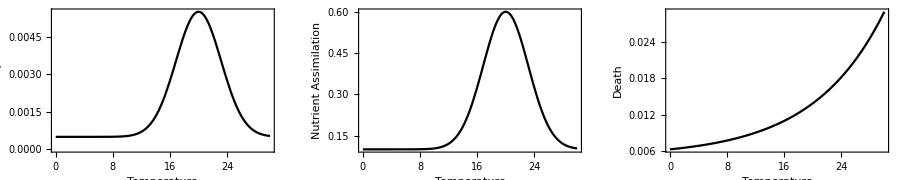

```mathematica
GraphicsRow[{
Plot[Vmax[T] /.T->temp/.par,{temp,0,30},ImageSize->300,Frame->True,Axes->True,PlotStyle->Black,FrameLabel->{"Temperature","Nutrient Uptake"}],
Plot[μinf[T]/. T->temp/.par,{temp,0,30},ImageSize->300,Frame->True,Axes->True,PlotStyle->Black,FrameLabel->{"Temperature","Nutrient Assimilation"}],
Plot[d[T]/. T->temp/.par,{temp,0,30},ImageSize->300,Frame->True,Axes->True,PlotStyle->Black,FrameLabel->{"Temperature","Death"}]},ImageSize->900]
```

```mathematica
TDroop[{R0_,Q0_,B0_,Z0_,start_:0}]:=Module[{transform={R->R[t],Q->Q[t],B->B[t],Z->Z[t]}},
{R'[t]==(fR/.transform),
Q'[t]==(fQ/.transform),
B'[t]==(fB/.transform),
Z'[t]==(fZ/.transform),
R[start]==R0,
Q[start]==Q0,
B[start]==B0,
Z[start]==Z0}
]
```

```mathematica
tmax=10000
```

10000

```mathematica
Clear[sol]
```

```mathematica
sol[R0_,Q0_,B0_,Z0_,temp_,r0val_]:=NDSolve[TDroop[{R0,Q0,B0,Z0}]/.T->temp/.r0->r0val/.par,{R,Q,B,Z},{t,0,tmax},AccuracyGoal->70,MaxStepSize->0.01,MaxSteps->100000000]
```

### TPC, Equilibrium curves & important reference points

```mathematica
eqs=FullSimplify[Solve[{fR==0,fQ==0,fB==0},{R,Q,B}]];
```

```mathematica
inteq=FullSimplify[eqs[[2]]];
```

```mathematica
Beqt=B/.inteq/.T->temp/.par;
```

```mathematica
Tmin=temp/.NSolve[Beqt==0&&0<temp<35,temp][[1]];
```

```mathematica
Tmax=temp/.NSolve[Beqt==0&&0<temp<35,temp][[2]];
```

```mathematica
Qmax=Vmax[T]/μinf[T]+Qmin;
```

#### Plot TPC (Figure 1B)

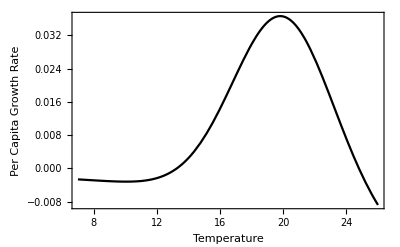

```mathematica
Plot[fB/B/.Q->Qmax/.par,{T,7,26},PlotStyle->Black,Frame->True,FrameLabel->{Style["Temperature",FontSize->14],Style["Per Capita Growth Rate",FontSize->14]}]
```

#### Plot equilibrium curve for reference (used in Figures 3, 4, and B1)

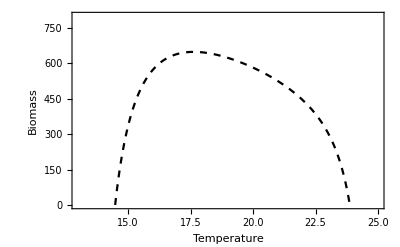

```mathematica
Plot[B/.inteq/.T->temp/.r0->0.5/.par,{temp,14,24.5},PlotStyle->{Black,Dashed,Thickness[0.004]},Frame->True,FrameLabel->{Style["Temperature",FontSize->14],Style[ "Biomass",FontSize->14]},Axes->False,PlotRange->{{13,25},{0,800}},ImageSize->400]
```

#### Figure B1

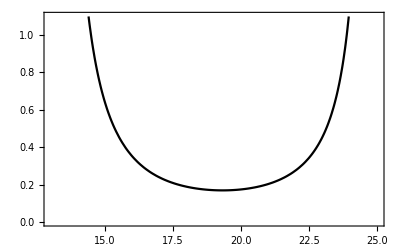
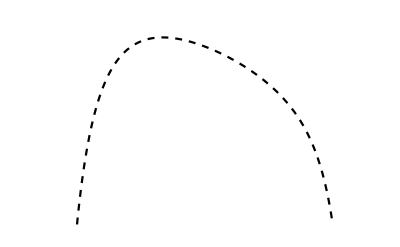
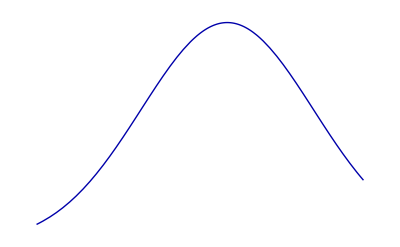
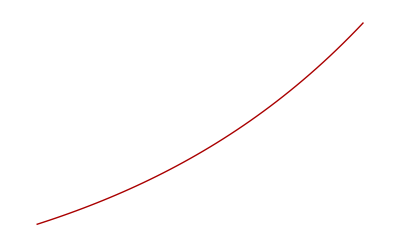

```mathematica
Overlay[{
Plot[R/.inteq/.T->temp/.r0->0.5/.par,{temp,13.5,24.5},PlotStyle->{Black,Thickness[0.004]},Frame->True,Axes->False,ImagePadding->30,PlotRange->{{13,25},{0,1.1}}],
Plot[B/.inteq/.T->temp/.r0->0.5/.par,{temp,13.5,24.5},PlotStyle->{Black,Dashed,Thickness[0.004]},Frame->False,Axes->False,ImagePadding->30,PlotRange->{{13,25},{0,700}}],
Plot[Vmax[T] /.T->temp/.par,{temp,13,25},PlotStyle->{Darker[Blue],Thickness[0.0025]},Frame->False,ImagePadding->30,Axes->False,PlotRange->{{13,25},All}],
Plot[d[T]/. T->temp/.par,{temp,13,25},PlotStyle->{Darker[Red],Thickness[0.0025]},Frame->False,ImagePadding->30,Axes->False,PlotRange->{{13,25},All}]
}]
```

#### r-K mismatch

```mathematica
Qeq=Q/.FullSimplify[Solve[fQ==0,Q]/.R->Rin/.Rin->1];
```

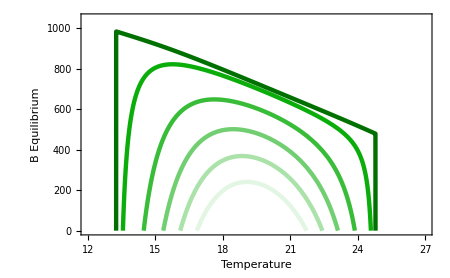
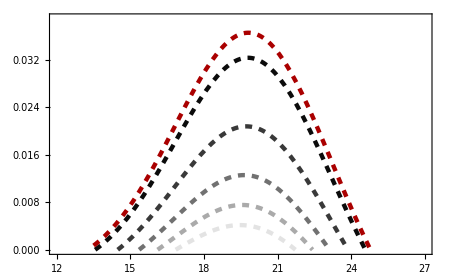

```mathematica
Overlay[{
Show[Table[{Plot[B/.inteq/.T->temp/.r0->r0val/.par,{temp,13.259515,24.790293},
FrameStyle->{Automatic,Darker[Green],Automatic,Automatic},Frame->{{True,False},{True,True}},Axes->True,FrameLabel->{Style["Temperature",FontSize->12,Bold],Style["B Equilibrium",FontSize->12,Bold]},
PlotStyle->{Directive[Darker[Green],Opacity[1-r0val/2.25],Thickness[0.007]]},
PlotRange->{{12,27},{0,1050}},ImageSize->450,ImagePadding->60]},
{r0val,{0.1,0.5,1,1.5,2}}],
Plot[B/.inteq/.T->temp/.r0->0.000001/.par,{temp,13.259515,24.790293},
FrameStyle->{Automatic,Darker[Green],Automatic,Automatic},Frame->{{True,False},{True,True}},Axes->True,FrameLabel->{Style["Temperature",FontSize->12,Bold],Style["B Equilibrium",FontSize->12,Bold]},
PlotStyle->{Directive[Darker[Darker[Green]],Thickness[0.007]]},
PlotRange->{{12,27},{0,1050}},ImageSize->450,ImagePadding->60]],
Show[Table[{Plot[fB/B/.Q->Qeq/.r0->r0val/.par,{T,13.5,24.75},PlotStyle->{Directive[Black,Dashed,Opacity[1-r0val/2.25],Thickness[0.007]]},Frame->{{False,True},{False,False}},FrameLabel->{{None,Style["dB/B*dt",FontSize->12,Bold]},{None,None}},FrameTicks->{{None,All},{None,None}},ImageSize->450,PlotRange->{{12,27},{0,0.039}},ImagePadding->60]},
{r0val,{0.1,0.5,1,1.5,2}}],
Plot[fB/B/.Q->Qmax/.par,{T,13.5,24.75},PlotStyle->{Directive[Darker[Red],Dashed,Thickness[0.007]]},Frame->{{False,True},{False,False}},FrameLabel->{{None,Style["dB/B*dt",FontSize->12,Bold]},{None,None}},FrameTicks->{{None,All},{None,None}},ImageSize->450,PlotRange->{{12,27},{0,0.039}},ImagePadding->60]]
}]
```

#### Figure 2C: r-K mismatch in 3C

```mathematica
Show[
ListLinePlot3D[Table[Join[{temp, B/.inteq/.T->temp/.r0->0.1/.par,0}],{temp,13.5,24.75,0.25}],PlotStyle->Darker[Darker[Darker[Green]]],PlotRange->{{12,26},{0,1000},{0,0.04}},ImageSize->550,BoxRatios->{1,1.5,0.5},Boxed->False,AxesStyle->Thickness[0.002],LabelStyle->Directive[FontOpacity->0],AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},
FaceGrids->{
{{0,-1,0},{{13,14,15,16,17,18,19,20,21,22,23,24,25,26},{0,0.01,0.02,0.03,0.04}}},
{{0,0,-1},{{13,14,15,16,17,18,19,20,21,22,23,24,25,26},{0,200,400,600,800,1000}}}
},FaceGridsStyle->Dashed],
ListLinePlot3D[Table[Join[{temp, B/.inteq/.T->temp/.r0->0.5/.par,0}],{temp,13.5,24.75,0.25}],PlotStyle->Darker[Darker[Green]],PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Table[Join[{temp, B/.inteq/.T->temp/.r0->1.0/.par,0}],{temp,13.5,24.75,0.25}],PlotStyle->Darker[Green],PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Table[Join[{temp, B/.inteq/.T->temp/.r0->1.5/.par,0}],{temp,13.5,24.75,0.25}],PlotStyle->Lighter[Lighter[Darker[Green]]],PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Table[Join[{temp, B/.inteq/.T->temp/.r0->2.0/.par,0}],{temp,13.5,24.75,0.25}],PlotStyle->Lighter[Lighter[Lighter[Darker[Green]]]],PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Table[Join[{temp, B/.inteq/.T->temp/.r0->2.75/.par,0}],{temp,13.5,24.75,0.25}],PlotStyle->Lighter[Lighter[Lighter[Lighter[Darker[Green]]]]],PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Table[Join[{temp, B/.inteq/.T->temp/.r0->0.000001/.par,0}],{temp,{13.259515,13.25952,13.2596,13.26,14,16,18,20,22,24,24.7,24.75,24.79028,24.790285,24.790288,24.79029,24.790292,24.790293}}],PlotStyle->Black,PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Partition[Flatten[Table[Join[{temp,0,fB/B/.Q->Qeq/.r0->0.1/.T->temp/.par}],{temp,13.25,24.75,0.25}]],3],PlotStyle->Black,PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Partition[Flatten[Table[Join[{temp,0,fB/B/.Q->Qeq/.r0->0.5/.T->temp/.par}],{temp,13.25,24.75,0.25}]],3],PlotStyle->Darker[Gray],PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Partition[Flatten[Table[Join[{temp,0,fB/B/.Q->Qeq/.r0->1.0/.T->temp/.par}],{temp,13.25,24.75,0.25}]],3],PlotStyle->Gray,PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Partition[Flatten[Table[Join[{temp,0,fB/B/.Q->Qeq/.r0->1.5/.T->temp/.par}],{temp,13.25,24.75,0.25}]],3],PlotStyle->Lighter[Gray],PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Partition[Flatten[Table[Join[{temp,0,fB/B/.Q->Qeq/.r0->2.0/.T->temp/.par}],{temp,13.25,24.75,0.25}]],3],PlotStyle->LightGray,PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Partition[Flatten[Table[Join[{temp,0,fB/B/.Q->Qeq/.r0->2.75/.T->temp/.par}],{temp,13.25,24.75,0.25}]],3],PlotStyle->Lighter[LightGray],PlotRange->{{12,26},{0,1000},{0,0.04}}],
ListLinePlot3D[Partition[Flatten[Table[Join[{temp,0,fB/B/.Q->Qmax/.T->temp/.par}],{temp,13.25,24.75,0.25}]],3],PlotStyle->Darker[Red],PlotRange->{{12,26},{0,1000},{0,0.04}}]
]
```

-Graphics3D-

### Effect of temperature and nutrient limitation on equilibria (numerical analysis) - Figure 2B

```mathematica
Tr0Bif[temp_,r0val_,r0max_]:=Module[{sol,solTrans,tstart,width=200,tend=5000,i0,crit,points},
tstart=tend-width;
solTrans=First@NDSolve[TDroop[{1,0.1,1,0}]/.T->temp/.r0->r0val/.par,{R,Q,B,Z},{t,0,tstart},AccuracyGoal->70,MaxStepSize->0.01,MaxSteps->1000000];
i0={R[tstart],Q[tstart],B[tstart],Z[tstart]}/.solTrans;
crit=WhenEvent[B'[t]==0,Sow[B[t]]];
{sol,points}=Reap@NDSolve[TDroop[i0]/.T->temp/.r0->r0val/.par,{R,Q,B},{t,0,width},MaxStepSize->0.01,MaxSteps->1000000];
If[Length[points]==0,
{{temp,1/r0val,First[B[width]/.sol]}}, 
Flatten[Thread[{temp,1/r0val,First[points]}]]
]
]
```

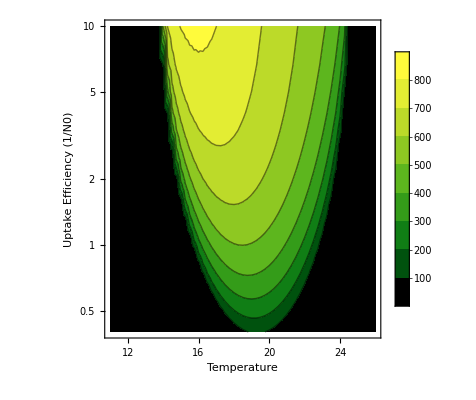

```mathematica
ListContourPlot[Flatten[ParallelTable[{Tr0Bif[temp,r0val,2.5]},{temp,11,26,0.25},{r0val,0.1,2.5,0.05}],3],
Frame->True,Axes->True,ScalingFunctions->{None,"Log"},ColorFunction->"AvocadoColors",FrameLabel->{Style["Temperature",FontSize->16,Bold],Style["Uptake Efficiency (1/N0)",FontSize->16,Bold]},PlotLegends->Automatic,LabelStyle->Directive[FontSize->14],Mesh->None]
```

```mathematica
Tr0QBif[temp_,r0val_,r0max_]:=Module[{sol,solTrans,tstart,width=100,tend=2000,i0,crit,points},
tstart=tend-width;
solTrans=First@NDSolve[TDroop[{1,0.1,1,0}]/.T->temp/.r0->r0val/.par,{R,Q,B,Z},{t,0,tstart},AccuracyGoal->70,MaxStepSize->0.01,MaxSteps->1000000];
i0={R[tstart],Q[tstart],B[tstart],Z[tstart]}/.solTrans;
crit=WhenEvent[Q'[t]==0,Sow[Q[t]]];
{sol,points}=Reap@NDSolve[TDroop[i0]/.T->temp/.r0->r0val/.par,{R,Q,B},{t,0,width},MaxStepSize->0.01,MaxSteps->1000000];
If[Length[points]==0,
{{temp,1/r0val,First[Q[width]/.sol]}}, 
Flatten[Thread[{temp,1/r0val,First[points]}]]
]
]
```

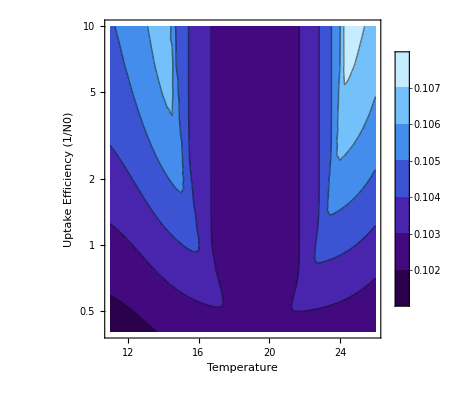

```mathematica
ListContourPlot[Flatten[ParallelTable[{Tr0QBif[temp,r0val,2.5]},{temp,11,26,0.25},{r0val,0.1,2.5,0.05}],3],
Frame->True,Axes->True,ScalingFunctions->{None,"Log"},FrameLabel->{Style["Temperature",FontSize->16,Bold],Style["Uptake Efficiency (1/N0)",FontSize->16,Bold]},PlotLegends->Automatic,LabelStyle->Directive[FontSize->14],ColorFunction->"DeepSeaColors"]
```

```mathematica
Tr0RBif[temp_,r0val_,r0max_]:=Module[{sol,solTrans,tstart,width=200,tend=5000,i0,crit,points},
tstart=tend-width;
solTrans=First@NDSolve[TDroop[{1,0.1,1,0}]/.T->temp/.r0->r0val/.par,{R,Q,B,Z},{t,0,tstart},AccuracyGoal->70,MaxStepSize->0.01,MaxSteps->1000000];
i0={R[tstart],Q[tstart],B[tstart],Z[tstart]}/.solTrans;
crit=WhenEvent[R'[t]==0,Sow[R[t]]];
{sol,points}=Reap@NDSolve[TDroop[i0]/.T->temp/.r0->r0val/.par,{R,Q,B},{t,0,width},MaxStepSize->0.01,MaxSteps->1000000];
If[Length[points]==0,
{{temp,1/r0val,First[R[width]/.sol]}}, 
Flatten[Thread[{temp,1/r0val,First[points]}]]
]
]
```

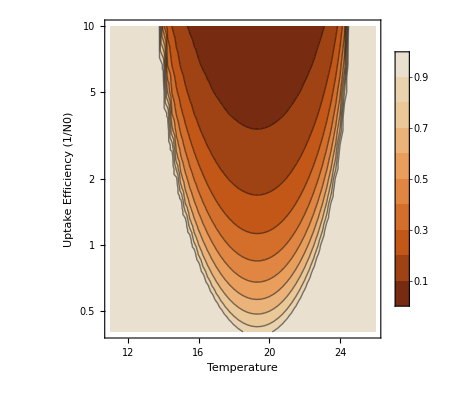

```mathematica
ListContourPlot[Flatten[ParallelTable[{Tr0RBif[temp,r0val,2.5]},{temp,11,26,0.25},{r0val,0.1,2.5,0.05}],3],
Frame->True,Axes->True,ScalingFunctions->{None,"Log"},FrameLabel->{Style["Temperature",FontSize->16,Bold],Style["Uptake Efficiency (1/N0)",FontSize->16,Bold]},PlotLegends->Automatic,LabelStyle->Directive[FontSize->14],ColorFunction->"SiennaTones"]
```

### Time series & transient dynamics (Figure 3)

```mathematica
prod[T_]:=μinf[T] (1-Qmin/Q)-d[T];
```

```mathematica
Toptr=temp/.FindMaximum[prod[T]/.Q->Qeq/.T->temp/.par,{temp,20}][[2]];
```

```mathematica
Toptk=temp/.FindMaximum[B/.inteq/.T->temp/.par,{temp,15}][[2]];
```

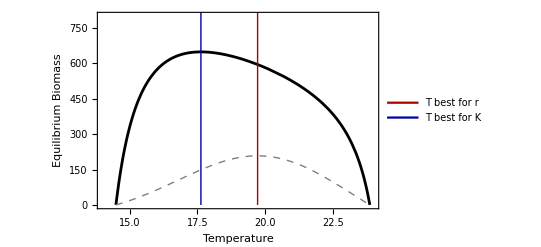

```mathematica
Show[{
Plot[B/.inteq/.T->temp/.r0->0.5/.par,{temp,0,26},PlotStyle->{Black,Thickness[0.005]},Frame->True,Axes->True,FrameLabel->{Style["Temperature",14],Style["Equilibrium Biomass",14]},PlotRange->{{14,24},{0,800}},PlotLegends->LineLegend[{Darker[Red],Darker[Blue]},{"T best for r","T best for K"}],ImageSize->400],
Plot[10000*fB/B/.Q->Qeq/.T->temp/.r0->0.5/.par,{temp,14,24},PlotStyle->{Gray,Dashed,Thickness[0.0025]},Frame->True,Axes->True,PlotRange->{{14,24},{0,800}}],
Graphics[{{Thickness[0.0025],Darker[Red],Line[{{Toptr,0},{Toptr,1000}}]}}],
Graphics[{{Thickness[0.0025],Darker[Blue],Line[{{Toptk,0},{Toptk,1000}}]}}]
}]
```

#### Force change temperature between Toptr and Toptk

```mathematica
Tchange[maxtemp_,change_,t0_,speed_]:=maxtemp-change /(1+Exp[-speed(t-t0)]);
```

```mathematica
Tchangesol[maxtemp_,change_,duration_,speed_]:=NDSolve[TDroop[{1,0.101,0.1,0}]/.T->Tchange[maxtemp,change,duration,speed]/.par,{R,Q,B},{t,0,tmax},MaxStepSize->0.01,MaxSteps->10000000];
```

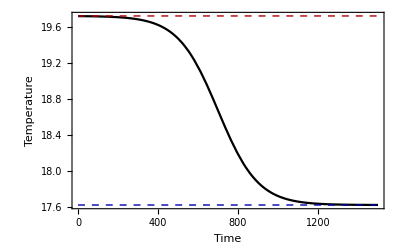

```mathematica
Show[{Plot[Tchange[Toptr,Toptr-Toptk,700,0.01],{t,0,1500},PlotStyle->Black,PlotRange->Full,Frame->True,FrameLabel->{Style["Time",14],Style["Temperature",14]}],
Graphics[{{Thickness[0.0025],Darker[Red],Dashed,Line[{{0,Toptr},{1500,Toptr}}]}}],
Graphics[{{Thickness[0.0025],Darker[Blue],Dashed,Line[{{0,Toptk},{1500,Toptk}}]}}]
}]
```

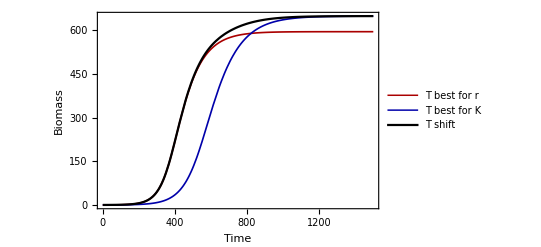

```mathematica
Show[
Plot[{Evaluate[B[t]/.sol[1,0.101,0.1,0,Toptr,0.5]],Evaluate[B[t]/.sol[1,0.101,0.1,0,Toptk,0.5]]},{t,0,1500},PlotRange->Full,PlotLegends->{"T best for r","T best for K"},Frame->True,PlotStyle->{{Darker[Red],Thickness[0.003]},{Darker[Blue],Thickness[0.003]}},FrameLabel->{Style["Time",14],Style["Biomass",14]}],
Plot[Evaluate[{B[t]}/.Tchangesol[Toptr,Toptr-Toptk,700,0.01]],{t,0,1500},PlotLegends->{"T shift"},PlotStyle->Black]
]
```

### Sinusoidally-varying temperature & dynamics (Figure 4)

Will need to define the amplitude and periodicity of temperature variation, to look at effects of varying rates of temperature warm ups in different temperature ranges.

Create a temperature function that is a sine function centred around some average temperature. Here, this is a function of average temperature, amplitude of variation and period, which we can use to vary temperature continuously. 
Using the plot below for reference, we can see that temp is the average temperature (around which the sine function operates), amplitude defines the temperature fluctuation above/below this average (e.g., a temp=20 & Amp=5 means that the temperature varies between 15 and 25 degrees), and period defines the number of time units (days?) for a full cycle period (i.e., 1/cycle frequency).

```mathematica
Clear[Tforce]
```

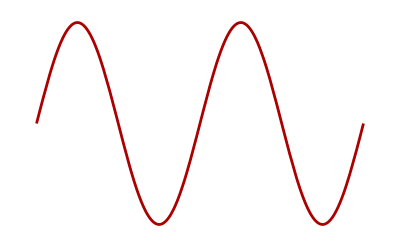

```mathematica
Tforce[temp_,Amp_,p_]:=temp+Amp Sin[(1/p 2 Pi) t];
Plot[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500],{t,0,1000},PlotStyle->{Darker[Red],Thickness[0.005]},Frame->False,Axes->False]
```

```mathematica
Tvar[temp_,amp_,per_,r0val_]:=NDSolve[TDroop[{1,0.1,1,0}]/.T->Tforce[temp,amp,per]/.r0->r0val/.par,{R,Q,B},{t,0,tmax},MaxStepSize->0.01,MaxSteps->∞];
```

```mathematica
tmax=1000000
```

1000000

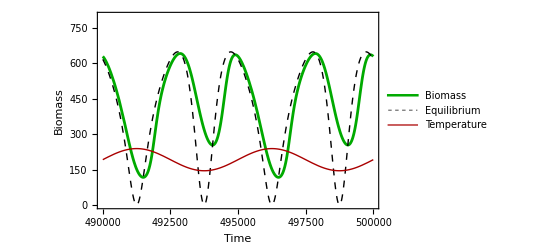

```mathematica
Show[Plot[Evaluate[{B[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000,r0/.par]],{t,490000,500000},PlotLegends->{"Biomass"},Frame->True,FrameLabel->{Style["Time",14],Style["Biomass",14]},PlotStyle->{Darker[Green],Thickness[.005]},PlotRange->{All,{0,800}},ImageSize->400],
Plot[Beqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000],{t,490000,500000},PlotStyle->{Black,Thickness[.0025],Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[10*Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000]/.par,{t,490000,500000},PlotStyle->{Darker[Red],Thickness[.0025]},PlotLegends->{"Temperature"}]]
```

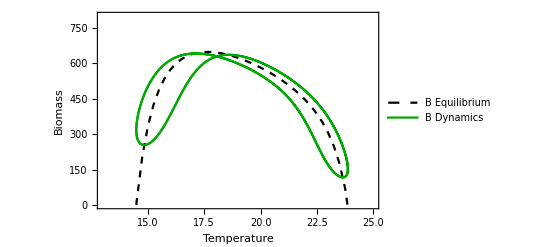

```mathematica
Show[ListPlot[Table[Join[{temp,B/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{{13,25},{0,800}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Biomass",14]},PlotLegends->{"B Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000],{t,20000,30000}],Flatten[Table[Evaluate[B[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000,0.5]],{t,20000,30000}]]],2],Joined->True,PlotStyle->Darker[Green],PlotLegends->{"B Dynamics"}]]
```

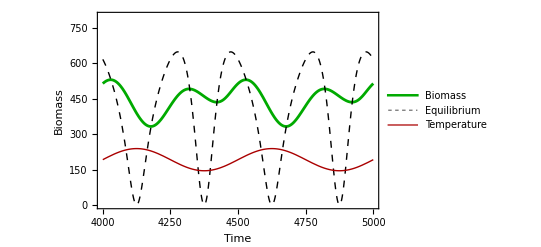

```mathematica
Show[Plot[Evaluate[{B[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500,r0/.par]],{t,4000,5000},PlotLegends->{"Biomass"},Frame->True,FrameLabel->{Style["Time",14],Style["Biomass",14]},PlotStyle->{Darker[Green],Thickness[.005]},PlotRange->{All,{0,800}},ImageSize->400],
Plot[Beqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500],{t,4000,5000},PlotStyle->{Black,Dashed,Thickness[.0025]},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[10*Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500]/.par,{t,4000,5000},PlotStyle->{Darker[Red],Thickness[.0025]},PlotLegends->{"Temperature"}]]
```

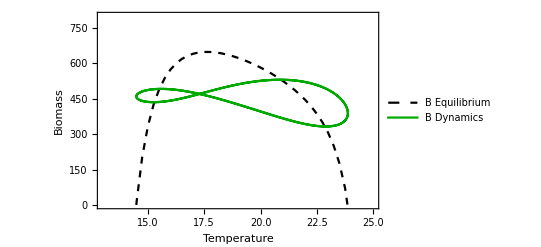

```mathematica
Show[ListPlot[Table[Join[{temp,B/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{{13,25},{0,800}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Biomass",14]},PlotLegends->{"B Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500],{t,4000,5000}],Flatten[Table[Evaluate[B[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500,0.5]],{t,4000,5000}]]],2],Joined->True,PlotStyle->Darker[Green],PlotLegends->{"B Dynamics"}]]
```

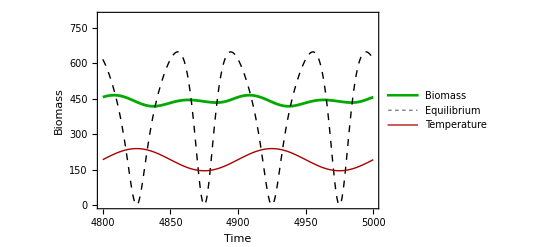

```mathematica
Show[Plot[Evaluate[{B[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100,r0/.par]],{t,4800,5000},PlotLegends->{"Biomass"},Frame->True,FrameLabel->{Style["Time",14],Style["Biomass",14]},PlotStyle->{Darker[Green],Thickness[.005]},PlotRange->{All,{0,800}},ImageSize->400],
Plot[Beqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100],{t,4800,5000},PlotStyle->{Black,Thickness[.0025],Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[10*Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100]/.par,{t,4800,5000},PlotStyle->{Darker[Red],Thickness[.0025]},PlotLegends->{"Temperature"}]]
```

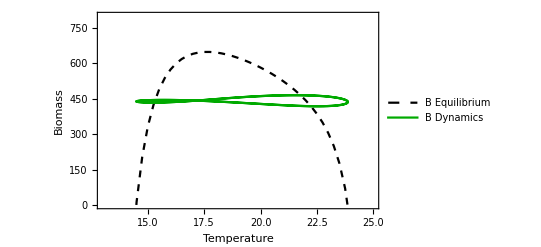

```mathematica
Show[ListPlot[Table[Join[{temp,B/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{{13,25},{0,800}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Biomass",14]},PlotLegends->{"B Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100],{t,4800,5000}],Flatten[Table[Evaluate[B[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100,0.5]],{t,4800,5000}]]],2],Joined->True,PlotStyle->Darker[Green],PlotLegends->{"B Dynamics"}]]
```

## Supplementary Figures

### Isoclines (Figure A1)

```mathematica
Riso=FullSimplify[B/.Solve[fR==0,B]/.Rin->1]
```

{-(ⅇ^((T-Toptv)^2/σv) (-1+R) (R+r0) δ)/(R (ⅇ^((T-Toptv)^2/σv) v0+v1))}

```mathematica
Qiso=FullSimplify[R/.Solve[fQ==0,R]];
```

```mathematica
Biso=FullSimplify[Q/.Solve[fB==0,Q]];
```

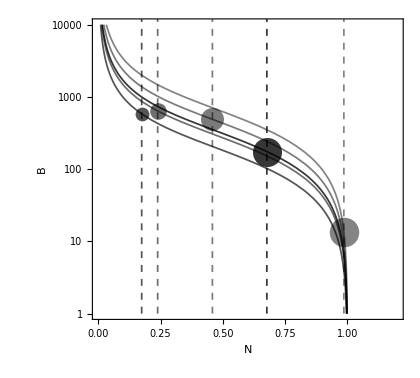

```mathematica
Show[Table[
Show[
Plot[Riso/.R->Rval/.T->temp/.par,{Rval,0,1.5},Frame->True,FrameLabel->{Style["N",Bold,14],Style["B",Bold,14]},ScalingFunctions->{None,"Log"},PlotRange->{{0,1.2},{1,10^4}},PlotStyle->{Black,Opacity[temp/30],Thickness[0.003]},ImageSize->420,AspectRatio->0.9],
Graphics[{
{Thickness[0.003],Black,Dashed,Opacity[temp/30],Line[{{Qiso[[1]]/.Q->Biso[[1]]/.T->temp/.par,0},{Qiso[[1]]/.Q->Biso[[1]]/.T->temp/.par,10}}]}
}],
Graphics[{
PointSize->(Biso[[1]]-0.1)/(0.11-0.1)*0.1/.T->temp/.par,Opacity[temp/30],Point[{Qiso[[1]]/.Q->Biso[[1]]/.T->temp/.par,Log[B/.inteq]/.T->temp/.par}]}]
],
{temp,{14.5,15.5,17,20,23.5}}]]
```

### r-K mismatch generality: parameters and underlying assumptions of thermal responses

#### Find temperature optima for biomass and for production, and calculate difference between the two

```mathematica
MisMatch[r0val_,Tasymm_]:=Module[{Tsol,MeanB,production,biomass,MaxProd,MaxBio,Tmin=1,Tmax=30,Tstep=0.05},
Tsol:=NDSolve[TDroop[{1,0.1,1,0}]/.T->temp/.r0->r0val/.Toptv->Tasymm*Toptb/.par,{R,Q,B},{t,0,2000},AccuracyGoal->70,MaxStepSize->0.01,MaxSteps->100000000];
biomass=Table[Join[{temp,Mean[Flatten[B[Range[1900,2000,0.01]]/.Tsol]]}],{temp,Tmin,Tmax,Tstep}];
production=Partition[Flatten[Table[Join[{temp,fB/B/.Q->Qeq/.r0->r0val/.T->temp/.Toptv->Tasymm*Toptb/.par}],{temp,Tmin,Tmax,Tstep}]],2];
MaxProd=production[[Flatten[Position[production,Max[production[[All,2]]]]][[1]]]];
MaxBio=biomass[[Flatten[Position[biomass,Max[biomass[[All,2]]]]][[1]]]];
MaxProd[[1]]-MaxBio[[1]]
]
```

```mathematica
MisMatch0[d0val_,v0val_,μ0val_]:=Module[{Tsol,MeanB,production,biomass,MaxProd,MaxBio,Tmin=1,Tmax=30,Tstep=0.05},
Tsol:=NDSolve[TDroop[{1,1,1,0}]/.T->temp/.d0->d0val/.v0->v0val/.μ0->μ0val/.par,{R,Q,B},{t,0,3000},AccuracyGoal->70,MaxStepSize->0.01,MaxSteps->100000000];
biomass=Table[Join[{temp,Mean[Flatten[B[Range[2900,3000,0.01]]/.Tsol]]}],{temp,Tmin,Tmax,Tstep}];
production=Partition[Flatten[Table[Join[{temp,fB/B/.Q->Qeq/.d0->d0val/.v0->v0val/.μ0->μ0val/.T->temp/.par}],{temp,Tmin,Tmax,Tstep}]],2];
MaxProd=production[[Flatten[Position[production,Max[production[[All,2]]]]][[1]]]];
MaxBio=biomass[[Flatten[Position[biomass,Max[biomass[[All,2]]]]][[1]]]];
MaxProd[[1]]-MaxBio[[1]]
]
```

#### Effect of other parameters on mismatch (Figure A2)

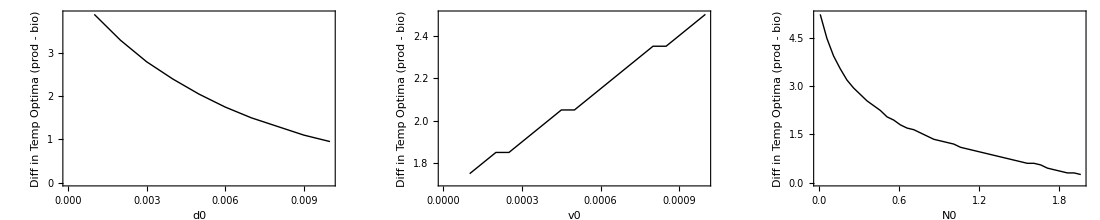

```mathematica
GraphicsRow[{
ListLinePlot[ParallelTable[Join[{d0val,MisMatch0[d0val,v0/.par,μ0/.par]}],{d0val,0.001,0.01,0.001}],Frame->True,Axes->True,FrameLabel->{"d0","Diff in Temp Optima (prod - bio)"},ImageSize->350,PlotStyle->{Black,Thick}],
ListLinePlot[ParallelTable[Join[{v0val,MisMatch0[d0/.par,v0val,μ0/.par]}],{v0val,0.0001,0.001,0.00005}],Frame->True,Axes->True,FrameLabel->{"v0","Diff in Temp Optima (prod - bio)"},ImageSize->350,PlotStyle->{Black,Thick}],
ListLinePlot[ParallelTable[Join[{r0val,MisMatch[r0val,1]}],{r0val,0.01,2,0.05}],Frame->True,Axes->True,FrameLabel->{"N0","Diff in Temp Optima (prod - bio)"},ImageSize->350,PlotStyle->{Black,Thick}]
},ImageSize->1100]
```

Note: for double exponential model (Figure A3), un-comment functions for uptake and mortality above, and recreate Figure 3C from main text

#### Effect of thermal asymmetry between uptake and assimilation (Figure A4 & A5)

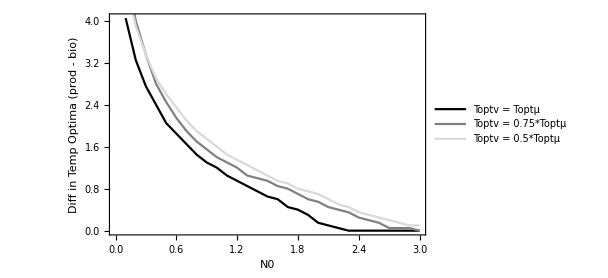

```mathematica
Show[{
ListLinePlot[ParallelTable[Join[{r0val,MisMatch[r0val,1]}],{r0val,0.1,3,0.1}],Frame->True,Axes->True,FrameLabel->{"N0","Diff in Temp Optima (prod - bio)"},ImageSize->450,PlotStyle->{Black,Thick},PlotLegends->LineLegend[{Black,Gray,LightGray},{"Toptv = Toptμ","Toptv = 0.75*Toptμ","Toptv = 0.5*Toptμ"}]],
ListLinePlot[ParallelTable[Join[{r0val,MisMatch[r0val,0.75]}],{r0val,0.1,3,0.1}],Frame->True,Axes->True,FrameLabel->{"N0","Diff in Temp Optima (prod - bio)"},ImageSize->450,PlotStyle->{Gray,Thick}],
ListLinePlot[ParallelTable[Join[{r0val,MisMatch[r0val,0.5]}],{r0val,0.1,3,0.1}],Frame->True,Axes->True,FrameLabel->{"N0","Diff in Temp Optima (prod - bio)"},ImageSize->450,PlotStyle->{LightGray,Thick}]
}]
```

```mathematica
Tsol[temp_,r0val_,Tasymm_]:=NDSolve[TDroop[{1,0.1,1,0}]/.T->temp/.r0->r0val/.Toptv->Tasymm*Toptb/.par,{R,Q,B},{t,0,1000},AccuracyGoal->70,MaxStepSize->0.01,MaxSteps->100000000];
biomass[r0val_,Tasymm_]:=ParallelTable[Join[{temp,Mean[Flatten[B[Range[900,1000,0.01]]/.Tsol[temp,r0val,Tasymm]]]}],{temp,1,30,0.1}];
```

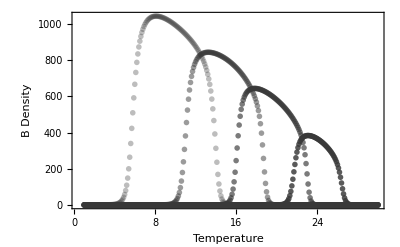

```mathematica
Show[Table[{ListPlot[biomass[r0/.par,asymm],
Frame->True,Axes->True,FrameLabel->{Style["Temperature",FontSize->12,Bold],Style["B Density",FontSize->12,Bold]},
PlotStyle->{Directive[Darker[Darker[Gray]],Opacity->asymm/1.5,PointSize[0.01]]},
PlotRange->{All,All},ImageSize->400]},{asymm,{0.5,0.75,1,1.25,1.5}}]]
```

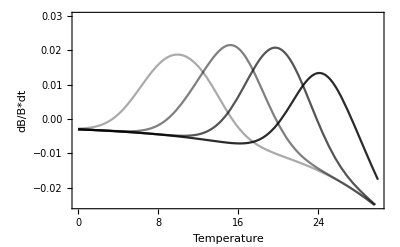

```mathematica
Show[Table[{Plot[fB/B/.Q->Qeq/.Toptv->asymm*Toptb/.par,{T,0,30},PlotStyle->{Directive[Black,Opacity[asymm/1.5],PointSize[0.01]]},Frame->True,FrameLabel->{"Temperature","dB/B*dt"},PlotRange->{All,{-0.025,0.03}},ImageSize->400]},{asymm,{0.5,0.75,1,1.25}}]]
```

### Eigenvalue solutions (Figure A6)

From the above equations we can generate the Jacobian and determine local stability of the trivial (axial, B=0) and nontrivial (interior, B>0) solutions:

```mathematica
jac=Outer[D,{fR,fQ,fB},{R,Q,B}];
```

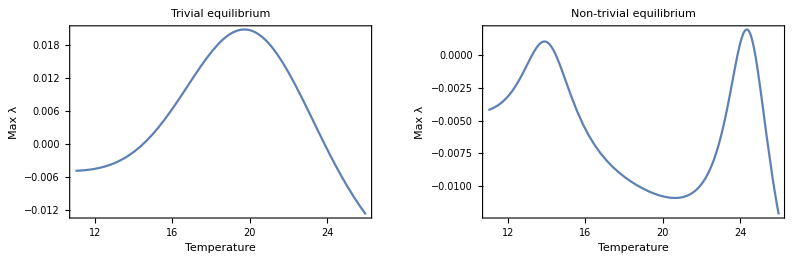

```mathematica
GraphicsRow[{Plot[Max[Eigenvalues[jac/.eqs[[1]]/.T->temp/.par]],{temp,11,26},PlotRange->All,Frame->True,FrameLabel->{"Temperature","Max λ"},PlotLabel->"Trivial equilibrium" ],
Plot[Max[Eigenvalues[jac/.eqs[[2]]/.T->temp/.par]],{temp,11,26},PlotRange->All,Frame->True,FrameLabel->{"Temperature","Max λ"},PlotLabel->"Non-trivial equilibrium" ]},ImageSize->800]
```

### Additional dynamics with periodic variation in temperature

#### Extreme slow and fast temperature variation and B dynamics (Figure A7)

period = 50 000

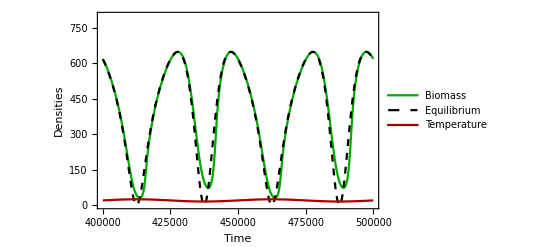

```mathematica
Show[Plot[Evaluate[{B[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,50000,r0/.par]],{t,400000,500000},PlotLegends->{"Biomass"},Frame->True,FrameLabel->{"Time","Densities"},PlotStyle->Darker[Green],PlotRange->{All,{0,800}},ImageSize->400],
Plot[Beqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,50000],{t,400000,500000},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,50000]/.par,{t,400000,500000},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

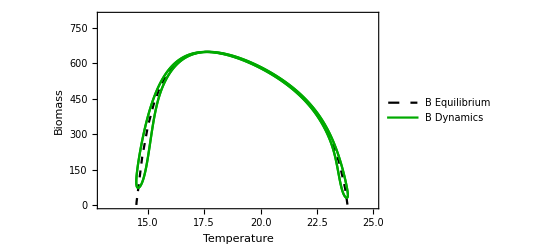

```mathematica
Show[ListPlot[Table[Join[{temp,B/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{{13,25},{0,800}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Biomass",14]},PlotLegends->{"B Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,50000],{t,200000,300000}],Flatten[Table[Evaluate[B[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,50000,0.5]],{t,200000,300000}]]],2],Joined->True,PlotStyle->Darker[Green],PlotLegends->{"B Dynamics"}]]
```

period = 10

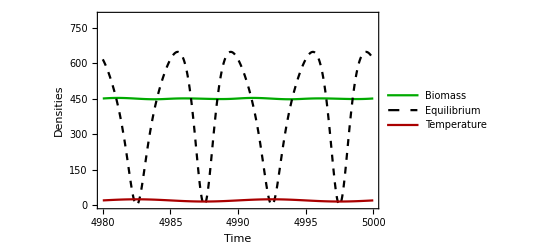

```mathematica
Show[Plot[Evaluate[{B[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,10,r0/.par]],{t,4980,5000},PlotLegends->{"Biomass"},Frame->True,FrameLabel->{"Time","Densities"},PlotStyle->Darker[Green],PlotRange->{All,{0,800}},ImageSize->400],
Plot[Beqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,10],{t,4980,5000},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,10]/.par,{t,4980,5000},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

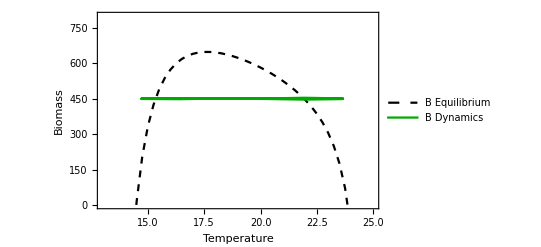

```mathematica
Show[ListPlot[Table[Join[{temp,B/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{{13,25},{0,800}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Biomass",14]},PlotLegends->{"B Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,10],{t,2000,2020}],Flatten[Table[Evaluate[B[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,10,0.5]],{t,2000,2020}]]],2],Joined->True,PlotStyle->Darker[Green],PlotLegends->{"B Dynamics"}]]
```

#### N dynamics with variable temperature (Figure A8)

```mathematica
Reqt=R/.inteq/.T->temp/.par;
```

period = 5000

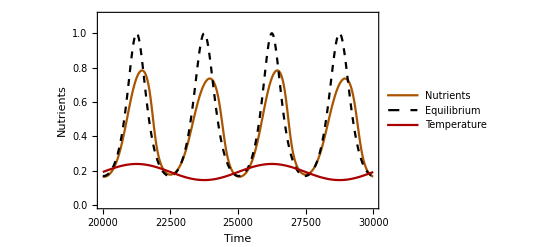

```mathematica
Show[Plot[Evaluate[{R[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000,r0/.par]],{t,20000,30000},PlotLegends->{"Nutrients"},Frame->True,FrameLabel->{"Time","Nutrients"},PlotStyle->Darker[Orange],PlotRange->{All,{0.0,1.1}},ImageSize->400],
Plot[Reqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000],{t,20000,30000},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[0.01*Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000]/.par,{t,20000,30000},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

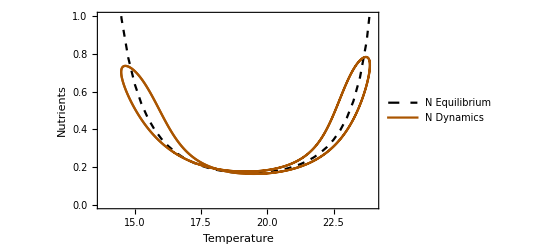

```mathematica
Show[ListPlot[Table[Join[{temp,R/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{All,{0.0,1}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Nutrients",14]},PlotLegends->{"N Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000],{t,20000,30000}],Flatten[Table[Evaluate[R[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000,0.5]],{t,20000,30000}]]],2],Joined->True,PlotStyle->Darker[Orange],PlotLegends->{"N Dynamics"}]]
```

period = 500

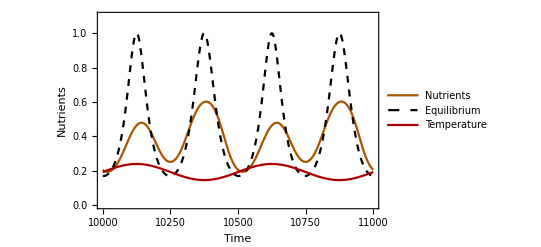

```mathematica
Show[Plot[Evaluate[{R[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500,r0/.par]],{t,10000,11000},PlotLegends->{"Nutrients"},Frame->True,FrameLabel->{"Time","Nutrients"},PlotStyle->Darker[Orange],PlotRange->{All,{0.0,1.1}},ImageSize->400],
Plot[Reqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500],{t,10000,11000},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[0.01*Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500]/.par,{t,10000,11000},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

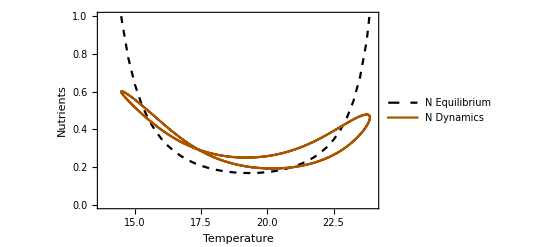

```mathematica
Show[ListPlot[Table[Join[{temp,R/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{All,{0.0,1}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Nutrients",14]},PlotLegends->{"N Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500],{t,10000,11000}],Flatten[Table[Evaluate[R[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500,0.5]],{t,10000,11000}]]],2],Joined->True,PlotStyle->Darker[Orange],PlotLegends->{"N Dynamics"}]]
```

period = 100

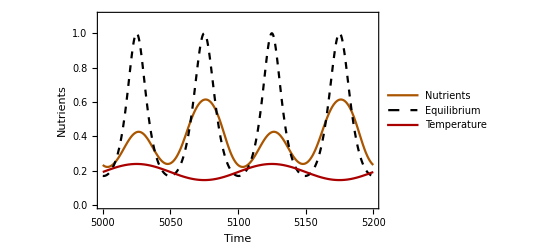

```mathematica
Show[Plot[Evaluate[{R[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100,r0/.par]],{t,5000,5200},PlotLegends->{"Nutrients"},Frame->True,FrameLabel->{"Time","Nutrients"},PlotStyle->Darker[Orange],PlotRange->{All,{0.0,1.1}},ImageSize->400],
Plot[Reqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100],{t,5000,5200},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[0.01*Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100]/.par,{t,5000,5200},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

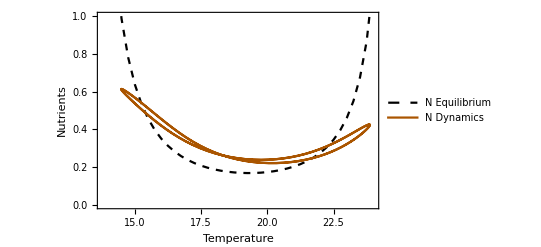

```mathematica
Show[ListPlot[Table[Join[{temp,R/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{All,{0.0,1}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Nutrients",14]},PlotLegends->{"N Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100],{t,5000,5200}],Flatten[Table[Evaluate[R[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100,0.5]],{t,5000,5200}]]],2],Joined->True,PlotStyle->Darker[Orange],PlotLegends->{"N Dynamics"}]]
```

#### Q dynamics with variable temperature (Figure A9)

```mathematica
Qeqt=Q/.inteq/.T->temp/.par
```

-(0.1 (0.5+0.1 ⅇ^(1/20 (-20+temp)^2)))/(-0.5+ⅇ^(1/20 (-20+temp)^2) (-0.095+0.0012 ⅇ^(0.1 temp)))

period = 5000

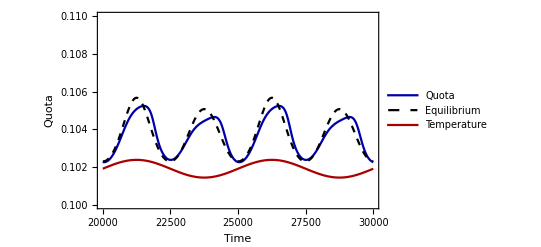

```mathematica
Show[Plot[Evaluate[{Q[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000,r0/.par]],{t,20000,30000},PlotLegends->{"Quota"},Frame->True,FrameLabel->{"Time","Quota"},PlotStyle->Darker[Blue],PlotRange->{All,{0.1,0.11}},ImageSize->400],
Plot[Qeqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000],{t,20000,30000},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[0.1+0.0001*Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000]/.par,{t,20000,30000},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

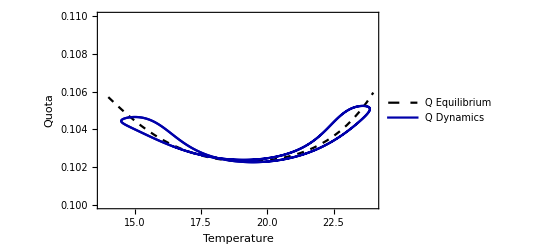

```mathematica
Show[ListPlot[Table[Join[{temp,Q/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{All,{0.1,0.11}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Quota",14]},PlotLegends->{"Q Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000],{t,20000,30000}],Flatten[Table[Evaluate[Q[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,5000,0.5]],{t,20000,30000}]]],2],Joined->True,PlotStyle->Darker[Blue],PlotLegends->{"Q Dynamics"}]]
```

period = 500

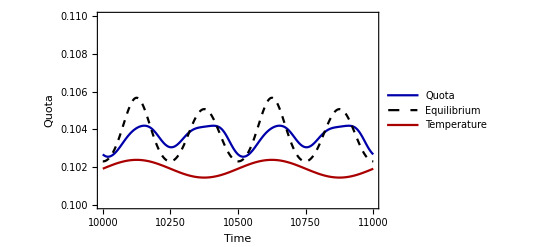

```mathematica
Show[Plot[Evaluate[{Q[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500,r0/.par]],{t,10000,11000},PlotLegends->{"Quota"},Frame->True,FrameLabel->{"Time","Quota"},PlotStyle->Darker[Blue],PlotRange->{All,{0.1,0.11}},ImageSize->400],
Plot[Qeqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500],{t,10000,11000},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[0.1+0.0001*Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500]/.par,{t,10000,11000},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

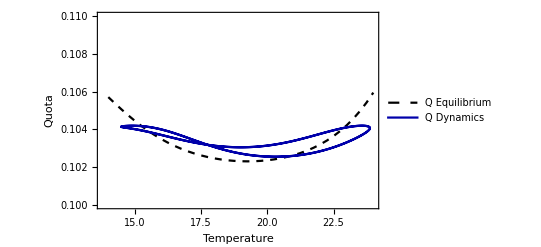

```mathematica
Show[ListPlot[Table[Join[{temp,Q/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{All,{0.1,0.11}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Quota",14]},PlotLegends->{"Q Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500],{t,10000,11000}],Flatten[Table[Evaluate[Q[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,500,0.5]],{t,10000,11000}]]],2],Joined->True,PlotStyle->Darker[Blue],PlotLegends->{"Q Dynamics"}]]
```

period = 100

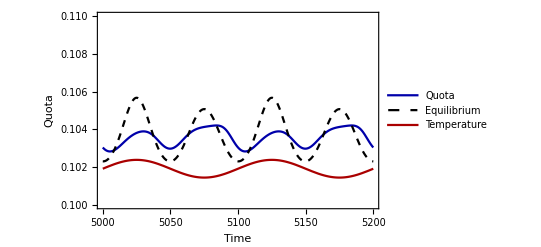

```mathematica
Show[Plot[Evaluate[{Q[t]}/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100,r0/.par]],{t,5000,5200},PlotLegends->{"Quota"},Frame->True,FrameLabel->{"Time","Quota"},PlotStyle->Darker[Blue],PlotRange->{All,{0.1,0.11}},ImageSize->400],
Plot[Qeqt/.temp->Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100],{t,5000,5200},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[0.1+0.0001*Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100]/.par,{t,5000,5200},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

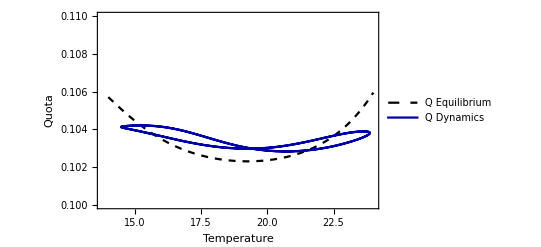

```mathematica
Show[ListPlot[Table[Join[{temp,Q/.inteq/.T->temp/.r0->0.5/.par}],{temp,14,24,0.25}],PlotRange->{All,{0.1,0.11}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Quota",14]},PlotLegends->{"Q Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100],{t,5000,5200}],Flatten[Table[Evaluate[Q[t]/.Tvar[Tmin+(Tmax-Tmin)/2,(Tmax-Tmin)/2,100,0.5]],{t,5000,5200}]]],2],Joined->True,PlotStyle->Darker[Blue],PlotLegends->{"Q Dynamics"}]]
```

#### Biomass dynamics with sinusoidally varying temperature temperatures surpass critical thresholds

period = 5000

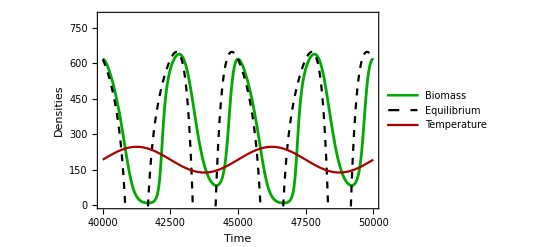

```mathematica
Show[Plot[Evaluate[{B[t]}/.Tvar[(Tmin-0.75)+((Tmax+0.75)-(Tmin-0.75))/2,((Tmax+0.75)-(Tmin-0.75))/2,5000,r0/.par]],{t,40000,50000},PlotLegends->{"Biomass"},Frame->True,FrameLabel->{"Time","Densities"},PlotRange->{All,{0,800}},PlotStyle->{Darker[Green],Thickness[.005]},ImageSize->400],
Plot[Beqt/.temp->Tforce[(Tmin-0.75)+((Tmax+0.75)-(Tmin-0.75))/2,((Tmax+0.75)-(Tmin-0.75))/2,5000],{t,40000,50000},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[10*Tforce[(Tmin-0.75)+((Tmax+0.75)-(Tmin-0.75))/2,((Tmax+0.75)-(Tmin-0.75))/2,5000]/.par,{t,40000,50000},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

period = 500

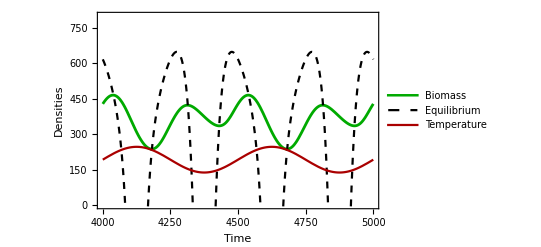

```mathematica
Show[Plot[Evaluate[{B[t]}/.Tvar[(Tmin-0.75)+((Tmax+0.75)-(Tmin-0.75))/2,((Tmax+0.75)-(Tmin-0.75))/2,500,r0/.par]],{t,4000,5000},PlotLegends->{"Biomass"},Frame->True,FrameLabel->{"Time","Densities"},PlotRange->{All,{0,800}},PlotStyle->{Darker[Green],Thickness[.005]},ImageSize->400],
Plot[Beqt/.temp->Tforce[(Tmin-0.75)+((Tmax+0.75)-(Tmin-0.75))/2,((Tmax+0.75)-(Tmin-0.75))/2,500],{t,4000,5000},PlotStyle->{Black,Dashed},Frame->True,PlotLegends->{"Equilibrium"},ImageSize->400],
Plot[10*Tforce[(Tmin-0.75)+((Tmax+0.75)-(Tmin-0.75))/2,((Tmax+0.75)-(Tmin-0.75))/2,500]/.par,{t,4000,5000},PlotStyle->Darker[Red],PlotLegends->{"Temperature"}]]
```

#### Nutrient limitation (N0=2) and B dynamics with variable temperature (Figure A11)

```mathematica
Beqt2=B/.inteq/.T->temp/.r0->2/.par;
```

```mathematica
Tmin2=temp/.NSolve[Beqt2==0&&0<temp<35,temp][[1]];
```

```mathematica
Tmax2=temp/.NSolve[Beqt2==0&&0<temp<35,temp][[2]];
```

period = 100

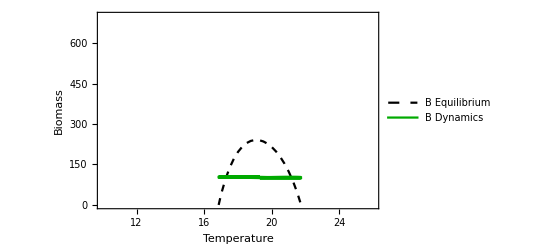

```mathematica
Show[ListPlot[Table[Join[{temp,B/.inteq/.T->temp/.r0->2/.par}],{temp,14,24,0.25}],PlotRange->{{10,26},{0,700}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Biomass",14]},PlotLegends->{"B Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin2+(Tmax2-Tmin2)/2,(Tmax2-Tmin2)/2,100],{t,3000,3200}],Flatten[Table[Evaluate[B[t]/.Tvar[Tmin2+(Tmax2-Tmin2)/2,(Tmax2-Tmin2)/2,100,2]],{t,3000,3200}]]],2],Joined->True,PlotStyle->Darker[Green],PlotLegends->{"B Dynamics"}]]
```

period = 500

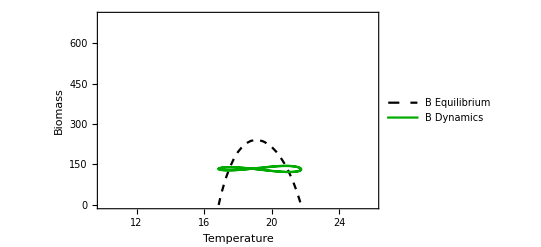

```mathematica
Show[ListPlot[Table[Join[{temp,B/.inteq/.T->temp/.r0->2/.par}],{temp,14,24,0.25}],PlotRange->{{10,26},{0,700}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Biomass",14]},PlotLegends->{"B Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin2+(Tmax2-Tmin2)/2,(Tmax2-Tmin2)/2,500],{t,5000,6000}],Flatten[Table[Evaluate[B[t]/.Tvar[Tmin2+(Tmax2-Tmin2)/2,(Tmax2-Tmin2)/2,500,2]],{t,5000,6000}]]],2],Joined->True,PlotStyle->Darker[Green],PlotLegends->{"B Dynamics"}]]
```

period = 5000

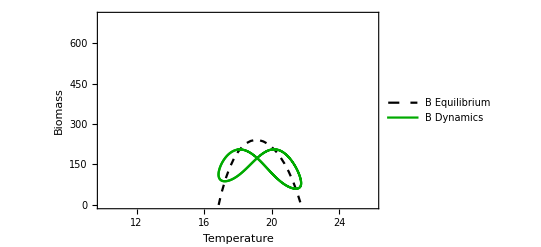

```mathematica
Show[ListPlot[Table[Join[{temp,B/.inteq/.T->temp/.r0->2/.par}],{temp,14,24,0.25}],PlotRange->{{10,26},{0,700}},Joined->True,PlotStyle->{Black,Dashed},Frame->True,FrameLabel->{Style["Temperature",14],Style["Biomass",14]},PlotLegends->{"B Equilibrium"},ImageSize->400],ListPlot[Partition[Riffle[Table[Tforce[Tmin2+(Tmax2-Tmin2)/2,(Tmax2-Tmin2)/2,5000],{t,20000,30000}],Flatten[Table[Evaluate[B[t]/.Tvar[Tmin2+(Tmax2-Tmin2)/2,(Tmax2-Tmin2)/2,5000,2]],{t,20000,30000}]]],2],Joined->True,PlotStyle->Darker[Green],PlotLegends->{"B Dynamics"}]]
```